## Initialization Code

```mathematica
nextReflectionPoint[{p_, dir_}, {a_,b_}] := 
Module[{solxy, distances,pos,x, y},
 solxy ={x, y}/.Quiet[Solve[{x == p[[1]] + s dir[[1]], 
         y== p[[2]] + s dir[[2]], 
x^2/a^2+y^2/b^2==1},{s,x,y}]];
distances = Norm[p-#]& /@ solxy;
pos=Position[distances,Max[distances]][[1]];
solxy[[#]]&@@pos
];
```

```mathematica
reflect[{p_, dir_},{a_, b_}] := 
Module[{normalDir,parallelDir,normalComponent,paralleComponent},
normalDir = -#/Norm[#]&[p/{a^2,b^2}];
parallelDir= Reverse[normalDir]{-1,1};
      normalComponent=normalDir.dir;
paralleComponent=parallelDir.dir;
{p,-normalComponent normalDir + paralleComponent parallelDir}
];
```

```mathematica
propagate[{p_, dir_},{a_, b_}] := 
Module[{p1},
p1=nextReflectionPoint[{p, dir}, {a,b}] ;
reflect[{p1, dir},{a, b}] 
];
```

```mathematica
makeStartData[φ_, α_,{a_,b_}] := 
Module[{p,normalDir,parallelDir},
p={a Cos[φ],b Sin[φ]};
normalDir = -#/Norm[#]&[p/{a^2,b^2}];
parallelDir= Reverse[normalDir]{-1,1};
{p, Cos[α] normalDir + Sin[α] parallelDir}
];
```

```mathematica
multiReflections[φ_, α_,n_, {a_,b_}] := 
NestList[propagate[#,{a, b}] &, makeStartData[φ, α,{a,b}] ,Round[n]];
```

```mathematica
ellipseMultiReflectionGraphics[φ_, α_,n_, {a_,b_}] := 
Module[{parameters,pathData,pathPoints},
parameters=N[Rationalize[{φ, α,n, {a,b}}, 0], 20 + 4 n];
pathData = multiReflections@@ parameters;
pathPoints = N[First /@ pathData];
Graphics[{{GrayLevel[0.95],Disk[{0,0},{a,b}]},
{Black,PointSize[0.016], N@If[a >=b,Point[{{Sqrt[a^2-b^2], 0}, {-Sqrt[a^2-b^2], 0}}],
Point[{{0, Sqrt[b^2-a^2] }, {0, -Sqrt[b^2-a^2] }}]]},
{Black,Thickness[0.006],Point[pathPoints[[1]]]},
{Black,PointSize[0.02],Circle[{0,0},{a,b}]},
{Thickness[0.005], MapIndexed[{Hue[0.3 #2[[1]]/n+.6],Line[#1]}&,
Partition[pathPoints,2,1]]}},PlotRange->All,ImageSize->{500,400}]
];
```

## Manipulate

```mathematica
Manipulate[
ellipseMultiReflectionGraphics[φ, α,n, {1,b}] ,
{{b, 1,"vertical half-axis length"}, 0.33, 3},
{{n, 10,"number of reflections"}, 1, 50, 1},
{{φ, 1,"starting position"},-Pi,Pi},
{{α,0,"starting angle"},-Pi/2+.01, Pi/2-.01},
SaveDefinitions->True,TrackedSymbols:>{b,n,φ,α}]
```

## Piancare

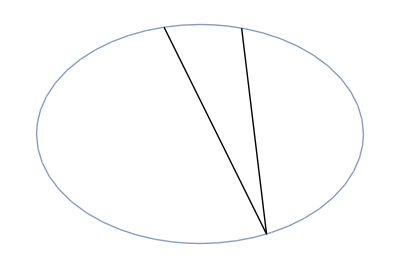

```mathematica
Show[Region@ImplicitRegion[{x^2/a^2+y^2/b^2==1},{x,y}],Graphics[Line/@collision[[;;1]]]]
```

```mathematica
collision=Partition[multiReflections[1.31319,0.295,3,{1,0.67}][[All,1]],3,1]
```

{{{0.254767,0.647892},{0.407042,-0.611984},{-0.219998,0.653585}},{{0.407042,-0.611984},{-0.219998,0.653585},{-0.423521,-0.606944}}}

```mathematica
col=collision[[1,2]]
```

{0.407042,-0.611984}

```mathematica
$Version
```

14.0.0 for Mac OS X ARM (64-bit) (December 13, 2023)

```mathematica
ArcLength@ImplicitRegion[{x^2+2 y^2==1,0<=x<=.5,-1<=y<=0},{x,y}]
```

Function::slotn: Slot number 2 in {Min[#1],Max[#2]}& cannot be filled from ({Min[#1],Max[#2]}&)[{{$Failed,$Failed},{$Failed,$Failed}}].

∞

```mathematica
ArcLength@ImplicitRegion[{x^2+y^2/0.67^2==1,col[[1]]<=x<=1,If[col[[2]]>0,0<=y<=col[[2]],col[[2]]<=y<=0]},{x,y}]
```

Function::slotn: Slot number 2 in {Min[#1],Max[#2]}& cannot be filled from ({Min[#1],Max[#2]}&)[{{$Failed,$Failed},{$Failed,$Failed}}].

∞

```mathematica
ArcLength[%]
```

Function::slotn: Slot number 2 in {Min[#1],Max[#2]}& cannot be filled from ({Min[#1],Max[#2]}&)[{{$Failed,$Failed},{$Failed,$Failed}}].

∞

```mathematica
arc[col_]:= ArcLength@ImplicitRegion[{x^2+y^2/0.67^2==1,col[[1]]<=x<=1,If[col[[2]]>0,0<=y<=col[[2]],col[[2]]<=y<=0]},{x,y}]
```

Since there is not collision for the last point and also first point, then for arc length calculations, we will not consider them:

```mathematica
s=arc/@collision[[All,2]];
ℒ=ArcLength@ImplicitRegion[x^2+y^2/.67^2==1,{x,y}];
```

Function::slotn: Slot number 2 in {Min[#1],Max[#2]}& cannot be filled from ({Min[#1],Max[#2]}&)[{{$Failed,$Failed},{$Failed,$Failed}}].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

```mathematica
θ=1/2(Module[{q1,p,q2},
{q1,p,q2}=#;Sign[Cross[Append[0][p-q1],Append[0][q2-p]][[-1]]]]PlanarAngle[#])&/@collision;
```

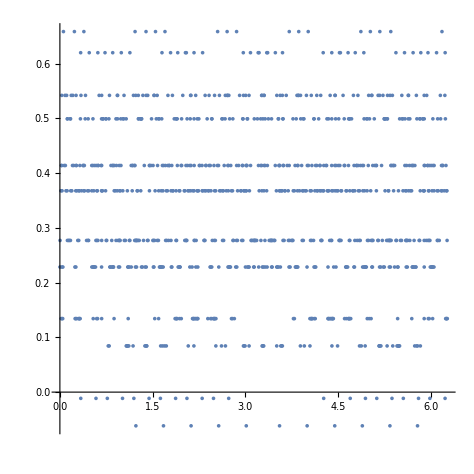

```mathematica
ListPlot[Transpose[{s,Sin[θ]}],AspectRatio->1,PlotRange->All]
```

```mathematica
Transpose[{s/ℒ,Sin[θ]}][[;;2]]
```

{{0.567009,0.122761},{0.161434,0.669642}}

```mathematica
Manipulate[
inc=pnts[[;;Position[pnts,final[[st+1,1]]][[1,1]]]];
Row@{Graphics[{{edges,Opacity[.2],LightBlue,DiscretizeRegion@reg},{Green,PointSize[Large],Point[origin],Line[inc]},{Red,PointSize[Medium],Point[final[[1,1]]]},{Red,lines[[;;st]],Blue,Arrow[{final[[st,1]],final[[st+1,1]]}],Arrow[{final[[st+1,1]],final[[st+2,1]]}]}},ImageSize->Small],ListPlot[Transpose[{s/ℒ,Sin[θ]}][[;;st]]->Range[st],AspectRatio->1,PlotRange->{{0,1},{-1,1}},Frame->True,GridLines->Automatic,ImageSize->Small](*,{#,#[[2]]<0,Sin[#[[2]]]}&/@(Transpose[{s/ℒ,θ}][[;;st]])*)},{st,1,100,1}]
```

Part::partd: Part specification final[[18,1]] is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::span: 1 ;; {}[[1,1]] is not a valid Span specification. A Span
     specification should be 1, 2, or 3 machine-sized integers separated by
     ;;. (Any of the integers can be omitted or replaced with All.)

DiscretizeRegion::regp: 
   A correctly specified region expected at position 1 of 
    DiscretizeRegion[reg].

Part::partd: Part specification final[[1,1]] is longer than depth of object.

Part::take: Cannot take positions 1 through 17 in lines.

Part::partd: Part specification final[[17,1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Transpose::nmtx: 
                             3.32096  5.92661  2.19951  5.00424  1.66143
   The first two levels of {{-------, -------, -------, -------, -------, 
                                ℒ        ℒ        ℒ        ℒ        ℒ
      4.66672  1.12251  3.74545  0.000951284  2.82282  5.74077  2.48526
      -------, -------, -------, -----------, -------, -------, -------, 
         ℒ        ℒ        ℒ          ℒ          ℒ        ℒ        ℒ
               4.9437  1.72181  4.60599  1.18395  4.26816  1.22965
      <<981>>, ------, -------, -------, -------, -------, -------}, Sin[θ]}
                 ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
     cannot be transposed.

Part::take: Cannot take positions 1 through 17 in 
                3.32096  5.92661  2.19951  5.00424  1.66143  4.66672
    Transpose[{{-------, -------, -------, -------, -------, -------, 
                   ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
       1.12251  3.74545  0.000951284  2.82282  5.74077           4.9437
       -------, -------, -----------, -------, -------, <<982>>, ------, 
          ℒ        ℒ          ℒ          ℒ        ℒ                ℒ
       1.72181  4.60599  1.18395  4.26816  1.22965
       -------, -------, -------, -------, -------}, Sin[θ]}].
          ℒ        ℒ        ℒ        ℒ        ℒ

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[1 ;; 17]
     cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression Annotation[1 ;; 17, Charting`Private`Tag#2]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

3.32096  5.92661  2.19951  5.00424
ListPlot::lpn: Annotation[Transpose[{{-------, -------, -------, -------, 
                                         ℒ        ℒ        ℒ        ℒ
         1.66143  4.66672  1.12251  3.74545  0.000951284           <<7>>
         -------, -------, -------, -------, -----------, <<985>>, -----, 
            ℒ        ℒ        ℒ        ℒ          ℒ                  ℒ
         4.60599  1.18395  4.26816  1.22965
         -------, -------, -------, -------}, <<1>>}], Ch<<19>>1][[<<1>>]] is
            ℒ        ℒ        ℒ        ℒ
     not a list of numbers or pairs of numbers.

Part::partd: Part specification final[[18,1]] is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::span: 1 ;; {}[[1,1]] is not a valid Span specification. A Span
     specification should be 1, 2, or 3 machine-sized integers separated by
     ;;. (Any of the integers can be omitted or replaced with All.)

DiscretizeRegion::regp: 
   A correctly specified region expected at position 1 of 
    DiscretizeRegion[reg].

Part::partd: Part specification final[[1,1]] is longer than depth of object.

Part::take: Cannot take positions 1 through 17 in lines.

Part::partd: Part specification final[[17,1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Transpose::nmtx: 
                             3.32096  5.92661  2.19951  5.00424  1.66143
   The first two levels of {{-------, -------, -------, -------, -------, 
                                ℒ        ℒ        ℒ        ℒ        ℒ
      4.66672  1.12251  3.74545  0.000951284  2.82282  5.74077  2.48526
      -------, -------, -------, -----------, -------, -------, -------, 
         ℒ        ℒ        ℒ          ℒ          ℒ        ℒ        ℒ
               4.9437  1.72181  4.60599  1.18395  4.26816  1.22965
      <<981>>, ------, -------, -------, -------, -------, -------}, Sin[θ]}
                 ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
     cannot be transposed.

Part::take: Cannot take positions 1 through 17 in 
                3.32096  5.92661  2.19951  5.00424  1.66143  4.66672
    Transpose[{{-------, -------, -------, -------, -------, -------, 
                   ℒ        ℒ        ℒ        ℒ        ℒ        ℒ
       1.12251  3.74545  0.000951284  2.82282  5.74077           4.9437
       -------, -------, -----------, -------, -------, <<982>>, ------, 
          ℒ        ℒ          ℒ          ℒ        ℒ                ℒ
       1.72181  4.60599  1.18395  4.26816  1.22965
       -------, -------, -------, -------, -------}, Sin[θ]}].
          ℒ        ℒ        ℒ        ℒ        ℒ

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[1 ;; 17]
     cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression Annotation[1 ;; 17, Charting`Private`Tag#2]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

3.32096  5.92661  2.19951  5.00424
ListPlot::lpn: Annotation[Transpose[{{-------, -------, -------, -------, 
                                         ℒ        ℒ        ℒ        ℒ
         1.66143  4.66672  1.12251  3.74545  0.000951284           <<7>>
         -------, -------, -------, -------, -----------, <<985>>, -----, 
            ℒ        ℒ        ℒ        ℒ          ℒ                  ℒ
         4.60599  1.18395  4.26816  1.22965
         -------, -------, -------, -------}, <<1>>}], Ch<<19>>1][[<<1>>]] is
            ℒ        ℒ        ℒ        ℒ
     not a list of numbers or pairs of numbers.

```mathematica
ListPlot[Transpose[{s/ℒ,Sin[θ]}][[;;st]]->Range[st],AspectRatio->1,PlotRange->{{0,1},{-1,1}},Frame->True,GridLines->Automatic,ImageSize->Medium]
```

-Graphics-

### scratch paper

```mathematica
(*angle[step_]:=Module[{l,hl,q2,p,q1},
{l,hl}=Rest@step;
q2=l[[1,1]];p=hl[[1]];q1=hl[[1]]+hl[[2]];
PlanarAngle[p->{q1,q2}]]*)
```

```mathematica
Rationalize[angle[final[[2]]]/π,.01]
```

2/7

```mathematica
PlanarAngle[Partition[final[[All,1]],3,1][[1]]]/π/2
```

0.210338

```mathematica
step=final[[2]];
Graphics[{{edges,Opacity[.2],LightBlue,DiscretizeRegion@reg},{Blue,final[[1,-1]]},{Green,PointSize[Medium],Point@step[[1]]},{Red,step[[2;;]]}}]
```

-Graphics-

```mathematica
pnts=SortBy[DeleteDuplicates[Join[Flatten[boundaryEdges[reg][[All,1]],1],{origin},final[[All,1]]]],ArcTan[Sequence@@#]&];
pnts=RotateLeft[pnts,Position[pnts,origin][[1,1]]-1];
```

```mathematica
ArcLength[Line@pnts[[;;Position[pnts,final[[10,1]]][[1,1]]]]]
```

8.10974

```mathematica
MeshPrimitives[BoundaryDiscretizeRegion[StadiumShape[]],1]
```

{Line[{{1.,-1.},{1.14231,-0.989821}}],Line[{{1.14231,-0.989821},{1.28173,-0.959493}}],Line[{{1.28173,-0.959493},{1.41542,-0.909632}}],Line[{{1.41542,-0.909632},{1.54064,-0.841254}}],Line[{{1.54064,-0.841254},{1.65486,-0.75575}}],Line[{{1.65486,-0.75575},{1.75575,-0.654861}}],Line[{{1.75575,-0.654861},{1.84125,-0.540641}}],Line[{{1.84125,-0.540641},{1.90963,-0.415415}}],Line[{{1.90963,-0.415415},{1.95949,-0.281733}}],Line[{{1.95949,-0.281733},{1.98982,-0.142315}}],Line[{{1.98982,-0.142315},{2.,0.}}],Line[{{2.,0.},{1.98982,0.142315}}],Line[{{1.98982,0.142315},{1.95949,0.281733}}],Line[{{1.95949,0.281733},{1.90963,0.415415}}],Line[{{1.90963,0.415415},{1.84125,0.540641}}],Line[{{1.84125,0.540641},{1.75575,0.654861}}],Line[{{1.75575,0.654861},{1.65486,0.75575}}],Line[{{1.65486,0.75575},{1.54064,0.841254}}],Line[{{1.54064,0.841254},{1.41542,0.909632}}],Line[{{1.41542,0.909632},{1.28173,0.959493}}],Line[{{1.28173,0.959493},{1.14231,0.989821}}],Line[{{1.14231,0.989821},{1.,1.}}],Line[{{1.,1.},{-1.,1.}}],Line[{{-1.,1.},{-1.14231,0.989821}}],Line[{{-1.14231,0.989821},{-1.28173,0.959493}}],Line[{{-1.28173,0.959493},{-1.41542,0.909632}}],Line[{{-1.41542,0.909632},{-1.54064,0.841254}}],Line[{{-1.54064,0.841254},{-1.65486,0.75575}}],Line[{{-1.65486,0.75575},{-1.75575,0.654861}}],Line[{{-1.75575,0.654861},{-1.84125,0.540641}}],Line[{{-1.84125,0.540641},{-1.90963,0.415415}}],Line[{{-1.90963,0.415415},{-1.95949,0.281733}}],Line[{{-1.95949,0.281733},{-1.98982,0.142315}}],Line[{{-1.98982,0.142315},{-2.,0.}}],Line[{{-2.,0.},{-1.98982,-0.142315}}],Line[{{-1.98982,-0.142315},{-1.95949,-0.281733}}],Line[{{-1.95949,-0.281733},{-1.90963,-0.415415}}],Line[{{-1.90963,-0.415415},{-1.84125,-0.540641}}],Line[{{-1.84125,-0.540641},{-1.75575,-0.654861}}],Line[{{-1.75575,-0.654861},{-1.65486,-0.75575}}],Line[{{-1.65486,-0.75575},{-1.54064,-0.841254}}],Line[{{-1.54064,-0.841254},{-1.41542,-0.909632}}],Line[{{-1.41542,-0.909632},{-1.28173,-0.959493}}],Line[{{-1.28173,-0.959493},{-1.14231,-0.989821}}],Line[{{-1.14231,-0.989821},{-1.,-1.}}],Line[{{-1.,-1.},{1.,-1.}}]}

```mathematica
dg=BoundaryDiscretizeRegion[StadiumShape[]];
```

```mathematica
MeshCellIndex[dg,1]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46}}

```mathematica
lines=MeshPrimitives[dg,1];
```

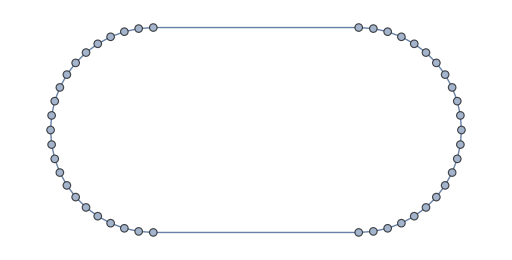

```mathematica
MeshConnectivityGraph[dg,0]
```

{{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30}}

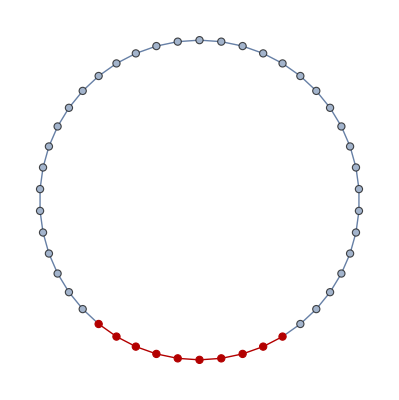

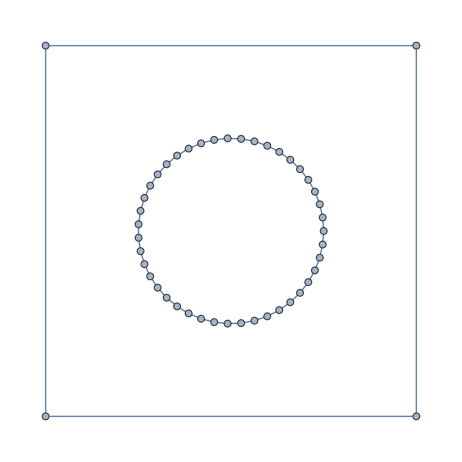

```mathematica
FindShortestPath[MeshConnectivityGraph[dg,1],{1,21},{1,30}]
HighlightGraph[MeshConnectivityGraph[dg,1],PathGraph[%]]
```

```mathematica
boundaryedgeindices=Flatten@Position[Length/@dg["ConnectivityMatrix"[1,2]]["AdjacencyLists"],1];
MeshPrimitives[dg,{1,boundaryedgeindices}]
```

```mathematica
dg["ConnectivityMatrix"]
```

MeshRegion::argnum: -- Message text not found -- (…)

Removed[$$Failure]